## Simple Code 1 No Spin

### Pieces

Normalizing the distribution

```mathematica
Integrate[x^2/(Exp[x/T]-1),{x,0,∞}]
```

ConditionalExpression[2 T^3 Zeta[3], Re[T]>0]

Creating the CDF

```mathematica
$Assumptions = {xi>0,T<1};
Simplify[Integrate[x^2/(Exp[x/T]-1),{x,0,xi}]/T^3/2/ Zeta[3]]
```

(xi^2 Log[1-ⅇ^(-xi/T)]-2 T (xi PolyLog[2,ⅇ^(-xi/T)]+T (PolyLog[3,ⅇ^(-xi/T)]-Zeta[3])))/(2 T^2 Zeta[3])

Plotting the CDF

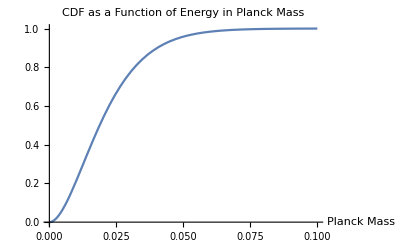

```mathematica
cdf[xi_]=(xi^2 Log[1-ⅇ^(-xi/T)]-2 T (xi PolyLog[2,ⅇ^(-xi/T)]+T (PolyLog[3,ⅇ^(-xi/T)]-Zeta[3])))/(2 T^2 Zeta[3]);
T=mp^2/8/π/M;(*This is in units of planck masses*)
Plot[cdf[xi]/.{mp->1,M->5},{xi,0,0.1},PlotRange->Full,PlotLabel->"CDF as a Function of Energy in Planck Mass",AxesLabel->{"Planck Mass"}](*'xi' is in units of planck masses*)
```

```mathematica
cdf[]
```

Creating a list of outputs from the CDF. The list will have 100 outputs evenly spaced in the x values (not the output values)

```mathematica
xin=0;
xf=0.1;(*xinitial and xfinal values*)
num=1000;(*Number of outputs in the list*)
div=(xf-xin)/num; (*the divisions between the x values up to the final value*)
outputs =Table[cdf[xi]/.{mp->1,M->5},{xi,xin,xf,div}];
inputs = Table[xi,{xi,xin,xf,div}];
```

Instead of having a table, make an array to hold both the outputs and the inputs (want to select an number from 0-1, find the bin and then subtract off the ‘xi’ value)

## How CDF changes with mass

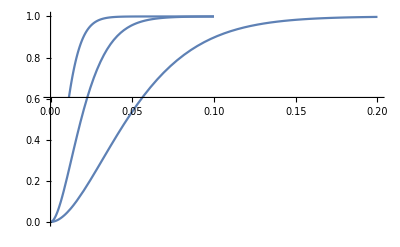

```mathematica
cdfexample[xi_]=(xi^2 Log[1-ⅇ^(-xi/T)]-2 T (xi PolyLog[2,ⅇ^(-xi/T)]+T (PolyLog[3,ⅇ^(-xi/T)]-Zeta[3])))/(2 T^2 Zeta[3]);
p10=Plot[cdfexample[xi]/.{mp->1,M->10},{xi,0,0.1}];
p5=Plot[cdfexample[xi]/.{mp->1,M->5},{xi,0,0.1}];
p2=Plot[cdfexample[xi]/.{mp->1,M->2},{xi,0,0.2}];
Show[{p10,p5,p2},PlotRange->Full]
```

## Creating a table with the single variable

```mathematica
Clear[cdf,xin,xf,num,div]
```

```mathematica
cdf[xibyT_]=(xibyT^2 Log[1-ⅇ^-xibyT]-2  (xibyT PolyLog[2,ⅇ^-xibyT]+(PolyLog[3,ⅇ^-xibyT]-Zeta[3])))/(2 Zeta[3]);
xin=0.000001;xf=12;num=10000;div=(xf-xin)/num;
cdflist=Table[{N[cdf[xibyT]],xibyT},{xibyT,xin,xf,div}];
```

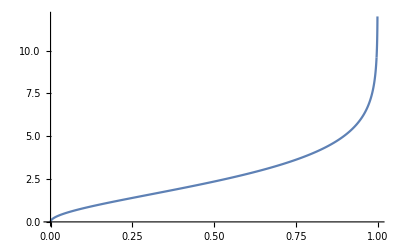

```mathematica
ListLinePlot[cdflist]
```

### Putting it all together

```mathematica
runs=2;
mass10=Table[5,{runs},{1}];
angular10=Table[0,{runs},{1}];
normangular10=Table[0,{runs},{1}];
xin=0.0000001;
xf=0.1;(*xinitial and xfinal values*)
num=1000;(*Number of outputs in the list*)
div=(xf-xin)/num; (*the divisions between the x values up to the final value*)
For[j=1,j<runs+1,j++,
For[i=1,i<1000,i++,
rand=RandomReal[];
y=mass10[[j,i]];
t1=Nearest[cdflist[[All,1]],rand];
t2=Part[t1,1];
t3=Flatten[Position[cdflist,t2]];
t4=Part[cdflist,t3[[1]]];
x=t4[[2]];
z=y-(x/8/π/y);
If[z<=0,Break[]];
AppendTo[mass10[[j]],z];
r2=RandomReal[];J=angular10[[j,i]];
If[J/y^2≥1,Break[]];
ρ=1/2-J/y^2;If[J>=1,If[r2≤ρ,AppendTo[angular10[[j]],J+1],AppendTo[angular10[[j]],J-1]],If[r2≤ρ,AppendTo[angular10[[j]],J+1],AppendTo[angular10[[j]],J]]];
If[J>0,If[r2≤ρ,AppendTo[normangular10[[j]],(J+1)/y^2],AppendTo[normangular10[[j]],(J-1)/y^2]],If[r2≤ρ,AppendTo[normangular10[[j]],(J+1)/y^2],AppendTo[normangular10[[j]],J/y^2]]];]]
```

```mathematica
normangular10
```

{{0,0,0.,0.,0.0408202,0.,0.,0.,0.0418722,0.,0.,0.,0.,0.,0.,0.,0.,0.0448705,0.0905829,0.045422,0.,0.,0.,0.,0.048,0.097311,0.0493877,0.0991684,0.150299,0.101223,0.0508327,0.10403,0.0522981,0.,0.,0.,0.0536508,0.107785,0.162752,0.111572,0.167983,0.114838,0.0575128,0.,0.,0.0603196,0.120961,0.184067,0.12506,0.063661,0.,0.0650043,0.130854,0.201866,0.274421,0.351171,0.428535,0.358324,0.293313,0.225011,0.152015,0.230258,0.156114,0.0794285,0.,0.,0.0835271,0.17093,0.0864634,0.176424,0.283606,0.190254,0.0966221,0.,0.,0.0984552,0.,0.10014,0.,0.103885,0.,0.,0.,0.115934,0.,0.,0.124482,0.263917,0.13541,0.275632,0.420563,0.290019,0.153109,0.,0.,0.17516,0.,0.186498,0.391399,0.198636,0.412711,0.211172,0.,0.233964,0.,0.268667,0.57539,0.308223,0.715506,0.390494,0.,0.,0.49127,0.,0.,0.,0.,1.06371},{0,1/25,0.0801929,0.040318,0.,0.0413507,0.0830039,0.125919,0.0844208,0.0429667,0.,0.,0.0438506,0.0890552,0.0450951,0.0908553,0.0460695,0.,0.0472747,0.0966275,0.0495155,0.100369,0.152024,0.204281,0.15395,0.103248,0.0517228,0.,0.,0.,0.,0.0543039,0.109711,0.168656,0.112569,0.169404,0.114675,0.17742,0.1192,0.0608467,0.12219,0.0615303,0.,0.,0.,0.0678245,0.,0.0691401,0.139136,0.211044,0.141951,0.0737762,0.,0.0751386,0.151765,0.0761479,0.,0.,0.,0.0805726,0.,0.,0.,0.,0.,0.,0.,0.0945506,0.,0.100797,0.,0.,0.,0.,0.,0.124478,0.252617,0.133242,0.,0.,0.,0.155977,0.324809,0.166767,0.,0.183679,0.,0.207025,0.456156,0.236726,0.,0.,0.290409,0.,0.,0.322908,0.667224,0.365584,0.,0.,0.454431,0.,0.,0.673893,0.,1.13072}}

```mathematica
Example={10,9,8};
For[i=1,i<3,i++,
If[Example[[i]]==9,Example[[i]]=1;Break[]]]
```

```mathematica
Example
```

{10,1,8}

# Speed Tweaks

## Filling the whole matrix before the calculation

```mathematica
run=1000;
```

```mathematica
depth=25;
mass2=Table[-1,{run},{depth}];
normangular2=Table[-1,{run},{depth}];
```

```mathematica
mass2[[All,1]]=2;
normangular2[[All,1]]=0;
```

```mathematica
For[j=1,j<run+1,j++,
For[i=1,i<depth+1,i++,
rand=RandomReal[];
y=mass2[[j,i]];(*Change here*)
t1=Nearest[cdflist[[All,1]],rand];
t2=Part[t1,1];
t3=Flatten[Position[cdflist,t2]];
t4=Part[cdflist,t3[[1]]];
x=t4[[2]];
z=y-(x/8/π/y);
If[z<=1,mass2[[j,i]]=1;Delete[normangular2,{j,i}];Break[],mass2[[j,i+1]]=z];(*Change Here*)
r2=RandomReal[];J=normangular2[[j,i]]; (*Change Here*)
If[J/y^2≥1,normangular2[[j,i]]=1;(*Change Here*)Break[]];
ρ=1/2-J;
If[J>J+(x/8/π/y)/y^2,If[r2≤ρ,normangular2[[j,i+1]]=J+(x/8/π/y)/y^2,normangular2[[j,i+1]]=J-(x/8/π/y)/y^2],If[r2≤ρ,normangular2[[j,i+1]]=J+(x/8/π/y)/y^2,normangular2[[j,i+1]]=J]];
If[J+(x/8/π/y)/y^2>1,normangular2[[j,i+1]]=1;Break[]];]]//AbsoluteTiming
```

{69.9489,Null}

## Previous way

```mathematica
Clear[mass2,normangular2]
```

```mathematica
run=1000;
depth=25;
```

```mathematica
mass2=Table[2,{run},{1}]; (*run=1000*)
normangular2=Table[0,{run},{1}];
For[j=1,j<run+1,j++,
For[i=1,i<depth+1,i++,
rand=RandomReal[];
y=mass2[[j,i]];(*Change here*)
t1=Nearest[cdflist[[All,1]],rand];
t2=Part[t1,1];
t3=Flatten[Position[cdflist,t2]];
t4=Part[cdflist,t3[[1]]];
x=t4[[2]];
xby8piy=(x/8/π/y);
z=y-xby8piy;
xby8piycubed=(x/8/π/y)/y^2;
If[z<=1,mass2[[j,i]]=1;Delete[normangular2,{j,i}];Break[]];
AppendTo[mass2[[j]],z];(*Change Here*)
r2=RandomReal[];J=normangular2[[j,i]]; (*Change Here*)
If[J/y^2≥1,normangular2[[j,i]]=1;Break[]];
ρ=1/2-J;
If[r2≤ρ,If[J+xby8piycubed>1,AppendTo[normangular2[[j]],1];Break[],AppendTo[normangular2[[j]],J+xby8piycubed]],AppendTo[normangular2[[j]],J-xby8piycubed]];]
]//AbsoluteTiming
```

{91.9957,Null}

## Interpolation

```mathematica
f[x_]=Sin[π*x]+3x;
table=Table[{f[x]},{x,0,10,0.2}];
```

```mathematica
g=Interpolation[table]
```

InterpolatingFunction[…]

```mathematica
g[2.1]
```

3.22

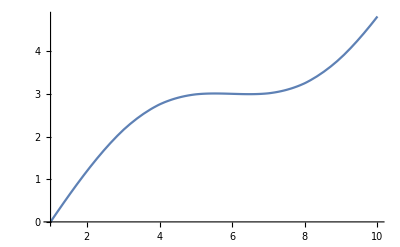

```mathematica
Plot[g[x],{x,1,10}]
```

```mathematica
h=InverseFunction[g]
```

InverseFunction[InterpolatingFunction[…]]

```mathematica
h[4]
```

9.18052

```mathematica
g[9.18]
```

3.99955

```mathematica
example=Table[{N[cdf[xibyT]],xibyT},{xibyT,xin,xf,div}];
ListLinePlot[example]
```

-Graphics-

```mathematica
run=1000;
mass2=Table[2,{run},{1}];
normangular2=Table[0,{run},{1}];
For[j=1,j<run+1,j++,
For[i=1,i<25,i++,
rand=RandomReal[];
y=mass2[[j,i]];(*Change here*)
x=cdflistinverse[rand];
z=y-(x/8/π/y);
If[z<=1,mass2[[j,i]]=1;Delete[normangular2,{j,i}];Break[]];
AppendTo[mass2[[j]],z];(*Change Here*)
r2=RandomReal[];J=normangular2[[j,i]]; (*Change Here*)
If[J/y^2≥1,normangular2[[j,i]]=1;Break[]];
ρ=1/2-J;
If[J>J+(x/8/π/y)/y^2,If[r2≤ρ,AppendTo[normangular2[[j]],J+(x/8/π/y)/y^2],AppendTo[normangular2[[j]],J-(x/8/π/y)/y^2]],If[r2≤ρ,AppendTo[normangular2[[j]],J+(x/8/π/y)/y^2],AppendTo[normangular2[[j]],J/y^2]]];
If[J+(x/8/π/y)/y^2>1,normangular2[[j,i+1]]=1;Break[]];]]//AbsoluteTiming
```

Part::partw: Part 2 of {{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},«990»} does not exist.

Part::partw: Part 2 of {0} does not exist.

Part::partw: Part 3 of {{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},«990»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
(*t1=Nearest[cdflist[[All,1]],rand];
t2=Part[t1,1];
t3=Flatten[Position[cdflist,t2]];
t4=Part[cdflist,t3[[1]]];
x=t4[[2]];*)
```